```mathematica
z[g_]:=n (
c (e-g) + g(a-b(n g))
);
n=8;
c=2;
a=31;
b=0.4;
e=12;
tablezall = N[Table[z[g],{g,0,12}],2];
tablezi = Table[z[g]/n,{g,0,12}];
Payoffs8 = Transpose[{tablezall,tablezi}];
part1 = Prepend[Payoffs8,{"Total Payoffs","Initial Payoffs"}];
part2 = MapThread[Prepend,{part1,{"Everyone (8) Invests","0",
"1","2","3","4","5","6","7","8","9","10","11","12"}}];
Grid[part2,
Spacings->{2,1},
Frame->All
]
```

Everyone (8) Invests | Total Payoffs | Initial Payoffs
0 | 192. | 24.
1 | 398.4 | 49.8
2 | 553.6 | 69.2
3 | 657.6 | 82.2
4 | 710.4 | 88.8
5 | 712. | 89.
6 | 662.4 | 82.8
7 | 561.6 | 70.2
8 | 409.6 | 51.2
9 | 206.4 | 25.8
10 | -48. | -6.
11 | -353.6 | -44.2
12 | -710.4 | -88.8

```mathematica
z[g_]:=n (
c (e-g) + g(a-b(n g))
);
n=5;
c=2;
a=31;
b=0.4;
e=12;
tablezall = Table[z[g],{g,0,12}];
tablezi = Table[z[g]/n,{g,0,12}];
Payoffs5 = Transpose[{tablezall,tablezi}];
part1 = Prepend[Payoffs5,{"Total Payoffs","Initial Payoffs"}];
part2 = MapThread[Prepend,{part1,{"Everyone (5) Invests","0",
"1","2","3","4","5","6","7","8","9","10","11","12"}}];
Grid[part2,
Spacings->{2,1},
Frame->All
]
```

Everyone (5) Invests | Total Payoffs | Initial Payoffs
0 | 120. | 24.
1 | 255. | 51.
2 | 370. | 74.
3 | 465. | 93.
4 | 540. | 108.
5 | 595. | 119.
6 | 630. | 126.
7 | 645. | 129.
8 | 640. | 128.
9 | 615. | 123.
10 | 570. | 114.
11 | 505. | 101.
12 | 420. | 84.

```mathematica
z[G_]:=a G-b G^2;
a=31;
b=0.4;
T =Table[z[G],{G,0,12*8}];
R = Range[0,12*8,1];
PlotTR = Transpose[{R,T}];
T2 =N[Table[z[G],{G,0,12*8,4}],0];
R2 = Range[0,12*8,4];
AccountPayoffs = Transpose[{R2,T2}];
part1 = Prepend[AccountPayoffs,{"Investment in the Account (# of tokens)","Total Payoffs"}];
Grid[part1,
Spacings->{2,1},
Frame->All
]
```

Investment in the Account (# of tokens) | Total Payoffs
0 | 0.
4 | 117.6
8 | 222.4
12 | 314.4
16 | 393.6
20 | 460.
24 | 513.6
28 | 554.4
32 | 582.4
36 | 597.6
40 | 600.
44 | 589.6
48 | 566.4
52 | 530.4
56 | 481.6
60 | 420.
64 | 345.6
68 | 258.4
72 | 158.4
76 | 45.6
80 | -80.
84 | -218.4
88 | -369.6
92 | -533.6
96 | -710.4

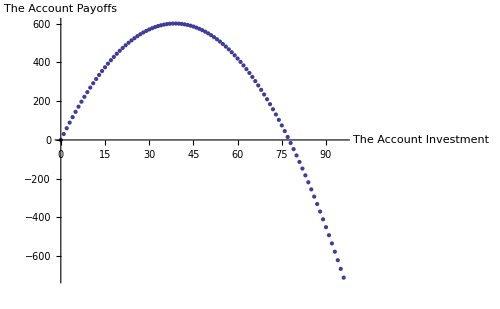

```mathematica
ListPlot[PlotTR,
AxesLabel->{"The Account Investment","The Account Payoffs"},
LabelStyle->{Bold,GrayLevel[0.3],11},
ImageSize->500
]
```